#### Graph coloring algorithm for FPGA ROSC design March 5, 2021 OPUS Lab confidential

## Read J-matrix from MATLAB

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
JJ=Import["./JOrig_0000.mat"];
(*hbias=Import["./h_0000.mat"];*)
JJ=Partition[Flatten[JJ],Dimensions[JJ][[2]],Dimensions[JJ][[2]]];
(*hbias=Flatten[hbias];*)
```

## Mathematica Built-in Graph Coloring

```mathematica
graph=AdjacencyGraph[Sign[Abs[JJ]]];
(*VertexDegree[graph]*) 
colorMap = FindVertexColoring[graph];
```

## Testing the algorithm:

Surprisingly total number of colors are usually much less than maximum degree of graphs (possibly for sparse) networks

```mathematica
Max[colorMap]
```

4

```mathematica
Export["colorMap.csv",{colorMap}]
```

colorMap.csv

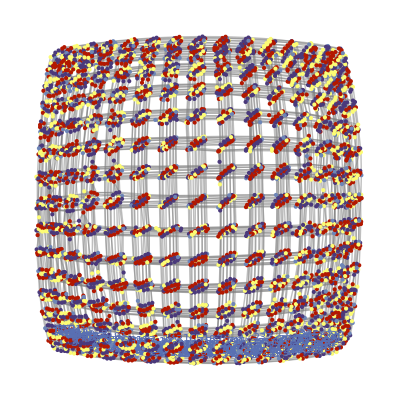

```mathematica
Graph[graph,EdgeStyle->Gray,VertexStyle->MapIndexed[First[#2]->ColorData[61,#1]&,colorMap],VertexLabels->Automatic]
```

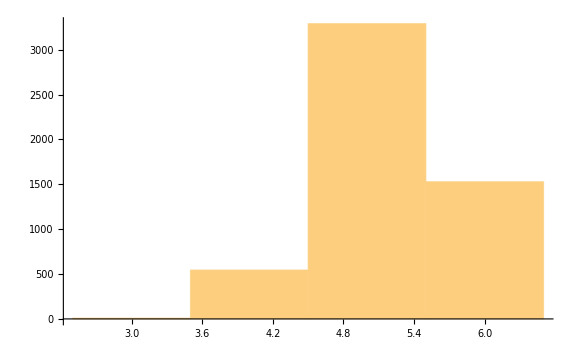

```mathematica
AdjacencyList[graph]//MatrixForm
Histogram[VertexDegree[graph],PlotRange->Full,ImageSize->Large]
```

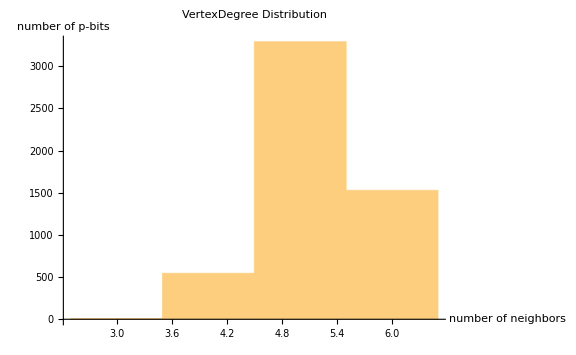

```mathematica
Show[%,AxesLabel->{HoldForm[number of neighbors],HoldForm[number of p-bits]},PlotLabel->HoldForm[VertexDegree Distribution],LabelStyle->{12,GrayLevel[0],Bold}]
```